# 1. Vaje - Rom

1. Naloga

```mathematica
(*a*)(1/3+1/6)^2
```

1/4

```mathematica
(*b*)3/(6/8)
```

4

```mathematica
(*c*)Sin[Pi/2]
```

1

```mathematica
(*d*)Exp[Log[7]]
```

7

2. Naloga

```mathematica
(*a*)((3+4x)/(2+5x))^2+((2+x)/(1-x))^2//FullSimplify
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

```mathematica
(*b*)x/y+y/x+2//FullSimplify
```

(x+y)^2/(x y)

```mathematica
(*c*)(x^2+y^2)^2-2(x y)^2//Simplify
```

x^4+y^4

```mathematica
(*d*)Sin[x]^2+Cos[x]^2//Simplify
```

1

```mathematica
(*e*)2Sin[x] Cos[x]//Simplify
```

Sin[2 x]

```mathematica
(*f*) Tan[Pi/8]^4 + (Cot[Pi/8])^4 // FullSimplify
```

34

```mathematica
(*g*)√(278+42 √5-12 √6-28 √30)//FullSimplify
```

3+7 √5-2 √6

3. Naloga

```mathematica
(x+xy+y)^10//TrigExpand
```

x^10+10 x^9 xy+45 x^8 xy^2+120 x^7 xy^3+210 x^6 xy^4+252 x^5 xy^5+210 x^4 xy^6+120 x^3 xy^7+45 x^2 xy^8+10 x xy^9+xy^10+10 x^9 y+90 x^8 xy y+360 x^7 xy^2 y+840 x^6 xy^3 y+1260 x^5 xy^4 y+1260 x^4 xy^5 y+840 x^3 xy^6 y+360 x^2 xy^7 y+90 x xy^8 y+10 xy^9 y+45 x^8 y^2+360 x^7 xy y^2+1260 x^6 xy^2 y^2+2520 x^5 xy^3 y^2+3150 x^4 xy^4 y^2+2520 x^3 xy^5 y^2+1260 x^2 xy^6 y^2+360 x xy^7 y^2+45 xy^8 y^2+120 x^7 y^3+840 x^6 xy y^3+2520 x^5 xy^2 y^3+4200 x^4 xy^3 y^3+4200 x^3 xy^4 y^3+2520 x^2 xy^5 y^3+840 x xy^6 y^3+120 xy^7 y^3+210 x^6 y^4+1260 x^5 xy y^4+3150 x^4 xy^2 y^4+4200 x^3 xy^3 y^4+3150 x^2 xy^4 y^4+1260 x xy^5 y^4+210 xy^6 y^4+252 x^5 y^5+1260 x^4 xy y^5+2520 x^3 xy^2 y^5+2520 x^2 xy^3 y^5+1260 x xy^4 y^5+252 xy^5 y^5+210 x^4 y^6+840 x^3 xy y^6+1260 x^2 xy^2 y^6+840 x xy^3 y^6+210 xy^4 y^6+120 x^3 y^7+360 x^2 xy y^7+360 x xy^2 y^7+120 xy^3 y^7+45 x^2 y^8+90 x xy y^8+45 xy^2 y^8+10 x y^9+10 xy y^9+y^10

```mathematica
Sin[x+y]//TrigExpand
```

Cos[y] Sin[x]+Cos[x] Sin[y]

4. Naloga

```mathematica
a = 3;
b = 4;
c = 6;
o = a + b+ c;
s = o/2;
√(s(s-a)(s-b)(s-c))(*ploščina trikotnika*)
```

(√455)/4

5. Naloga

```mathematica
s = {3,2,0,0,5,13,2,-x,8};
s[[5]]
s[[-1]]
```

5

8

6. Naloga

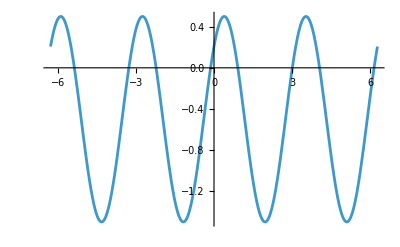

```mathematica
Plot[Sin[2x + Pi/4]-0.5, {x, -2Pi, 2Pi}]
```

7. Naloga

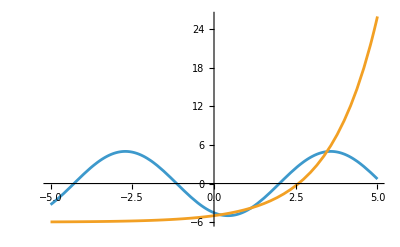

```mathematica
f[x_]:=5Sin[x-2]
g[x_]:=2^x - 6
Plot[{f[x],g[x]},{x, -5,5}]
```

```mathematica
FindRoot[f[x]==g[x],{x,3}]
```

Solve::naqs: -6+2^x is not a quantified system of equations and inequalities.

Solve::naqs: 2. is not a quantified system of equations and inequalities.

FindRoot::nlnum: The function value {-2.+Solve[2.]} is not a list of numbers with dimensions {1} at {x} = {3.}.

FindRoot[f[x]==g[x],{x,3}]

8. Naloga

```mathematica
a = 3^200 + 20;
b = 2^300 + 30;
a == b
a < b
a > b
```

False

False

True

9. Naloga

```mathematica
x^2 + 4x + 2 == 0 //Solve
```

{{x→-2-√2},{x→-2+√2}}

```mathematica
x^2 +4x+5 == 0 //Reduce
```

x==-2-ⅈ||x==-2+ⅈ

10. Naloga

```mathematica
x^4 == 1 //Reduce
```

x==-1||x==-ⅈ||x==ⅈ||x==1

```mathematica
x^4 == 1 // Solve
```

{{x→-1},{x→-ⅈ},{x→ⅈ},{x→1}}

11. Naloga

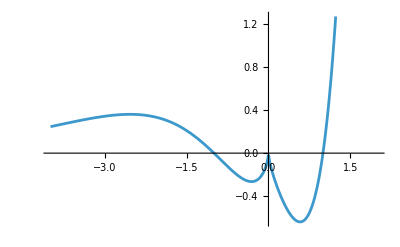

```mathematica
(*a*)h[x_]:=(x^2-(x^2)^(1/3))Exp[x]
(*b*)Plot[h[x],{x,-4,2}]
```

```mathematica
(*Ničle so -1, 0, 1*)
(*c*)Solve[h[x]==0,x]
```

{{x→0},{x→1}}

```mathematica
Reduce[h[x]==0,x]
```

x==-1||x==0||x==1